# Dynamical System of anisotropic tachyon model

## Packages and call parallel kernels

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[];
```

## System

## Dynamical variables

## Density parameters

```mathematica
ΩDE:=y^2/(√(1-x^2))+z^2+Σ^2
```

```mathematica
Ωm:=1-ΩDE-Ωr
```

## Cosmological parameters

```mathematica
q:=1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)
```

```mathematica
wDE:=-1+2/3(3/2(x^2 y^2)/(√(1-x^2))+2 z^2+3 Σ^2)/(y^2/(√(1-x^2))+z^2+Σ^2)
```

```mathematica
weff:=wDE ΩDE+1/3 Ωr
```

## Dynamical analytical analysis

## Autonomous set of equation

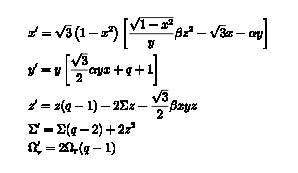

```mathematica
gx:=√3(1-x^2)((√(1-x^2))/y β z^2-√3 x-α y)
fx:=√3 β  z^2 √(1-x^2)-3x y-√3 α y^2
fy:=y((√3)/2 α y x+q+1)
fz:=z(q-1)-2Σ z-(√3)/2 β x y z
fS:=Σ(q-2)+2 z^2
fWr:=2Ωr(q-1)
```

#### Equations {x’,y’,z’,Σ’,Ωr’} under Transformation

```mathematica
Simplify[(-fx/.{x->-x,α->-α,β->-β})]
```

-3 x y-√3 y^2 α+√(3-3 x^2) z^2 β

```mathematica
(fy/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

y (1+q+1/2 √3 x y α)

```mathematica
(fz/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

(-1+q) z-1/2 √3 x y z β-2 z Σ

```mathematica
(fS/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

2 z^2+(-2+q) Σ

```mathematica
(fWr/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

2 (-1+q) Ωr

## Analytical dynamical analysis

```mathematica
Sol=Solve[{(fx/.√(1-x^2)->Γ)==0,(fy/.√(1-x^2)->Γ)==0,(fz/.√(1-x^2)->Γ)==0,(fS/.√(1-x^2)->Γ)==0,(fWr/.√(1-x^2)->Γ)==0},{x,y,z,Σ,Ωr}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[Sol]
```

25

### Classification of fixed points

```mathematica
Sol[[1]]
```

{y→0,z→0,Σ→0,Ωr→1}

```mathematica
Sol[[3]]
```

{y→0,z→0,Σ→0,Ωr→1}

```mathematica
Limit[weff,Sol[[1]]]
```

1/3

```mathematica
Sol[[2]]
```

{y→0,z→0,Σ→-1,Ωr→0}

```mathematica
Sol[[5]]
```

{y→0,z→0,Σ→1,Ωr→0}

```mathematica
Limit[weff,Sol[[2]]]
```

1

```mathematica
Limit[weff,Sol[[5]]]
```

1

```mathematica
Sol[[4]]
```

{y→0,z→0,Σ→0,Ωr→0}

```mathematica
Limit[weff,Sol[[4]]]
```

0

```mathematica
Sol[[6]]
```

{x→2/(√3),y→-2/α,z→0,Σ→0,Ωr→(α^2+12 Γ)/α^2}

```mathematica
Sol[[7]]
```

{x→-2/(√3),y→2/α,z→0,Σ→0,Ωr→(α^2+12 Γ)/α^2}

```mathematica
Sol[[8]]
```

{x→√2,y→-(√6)/α,z→0,Σ→-(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[9]]
```

{x→√2,y→-(√6)/α,z→0,Σ→(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[10]]
```

{x→-√2,y→(√6)/α,z→0,Σ→-(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[11]]
```

{x→-√2,y→(√6)/α,z→0,Σ→(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
√(1-x^2)/.x^2->4/3
```

ⅈ/(√3)

```mathematica
√(1-x^2)/.x^2->2
```

ⅈ

```mathematica
Sol[[12]]
```

{x→α/(√(α^2+3 Γ)),y→-(√3)/(√(α^2+3 Γ)),z→0,Σ→0,Ωr→0}

```mathematica
Sol[[13]]
```

{x→-α/(√(α^2+3 Γ)),y→(√3)/(√(α^2+3 Γ)),z→0,Σ→0,Ωr→0}

```mathematica
{fx,fy,fz,fWr,fS}/.{Ωr->0,Σ->0,z->0}
```

{-3 x y-√3 y^2 α,y (1+1/2 (1-3 √(1-x^2) y^2)+1/2 √3 x y α),0,0,0}

```mathematica
Solve[{(fx/.{Ωr->0,Σ->0,z->0})==0,(fy/.{Ωr->0,Σ->0,z->0})==0},{x,y}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0},{x→-1,y→(√3)/α},{x→1,y→-(√3)/α},{x→-(α √(-α^2-√(36+α^4)))/(3 √2),y→(√(-α^2-√(36+α^4)))/(√6)},{x→(α √(-α^2-√(36+α^4)))/(3 √2),y→-(√(-α^2-√(36+α^4)))/(√6)},{x→-(α √(-α^2+√(36+α^4)))/(3 √2),y→(√(-α^2+√(36+α^4)))/(√6)},{x→(α √(-α^2+√(36+α^4)))/(3 √2),y→-(√(-α^2+√(36+α^4)))/(√6)}}

```mathematica
Sol[[14]]
```

{x→(4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ),y→-(√(8+β^2 Γ))/(√2 α),z→-(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[15]]
```

{x→(4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ),y→-(√(8+β^2 Γ))/(√2 α),z→(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[16]]
```

{x→(4 √2 √(8+β^2 Γ))/(-8 √3-√3 β^2 Γ),y→(√(8+β^2 Γ))/(√2 α),z→-(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[17]]
```

{x→(4 √2 √(8+β^2 Γ))/(-8 √3-√3 β^2 Γ),y→(√(8+β^2 Γ))/(√2 α),z→(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Simplify[((4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ))^2,{Γ>0,β∈Reals}]
```

32/(24+3 β^2 Γ)

```mathematica
Solx2=Solve[χ==32/(24+3 β^2 √(1-χ)),χ]/.χ->x^2
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x^2→(-64+β^4)/(3 β^4)-(-331776-31104 β^4-81 β^8)/(243 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))+((-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(3 β^4)},{x^2→(-64+β^4)/(3 β^4)+((1+ⅈ √3) (-331776-31104 β^4-81 β^8))/(486 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))-((1-ⅈ √3) (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(6 β^4)},{x^2→(-64+β^4)/(3 β^4)+((1-ⅈ √3) (-331776-31104 β^4-81 β^8))/(486 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))-((1+ⅈ √3) (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(6 β^4)}}

```mathematica
Solx2[[1,1]]
```

x^2→(-64+β^4)/(3 β^4)-(-331776-31104 β^4-81 β^8)/(243 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))+((-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(3 β^4)

```mathematica
Reduce[(Solx2[[1,1,2]]>0)&&(4096 β^12+384 β^16-3 β^20>0),β]
```

False

```mathematica
Sol[[18]]
```

```mathematica
Sol[[19]]
```

```mathematica
Sol[[20]]
```

```mathematica
Sol[[21]]
```

```mathematica
Sol[[22]]
```

```mathematica
Sol[[23]]
```

```mathematica
Sol[[24]]
```

```mathematica
Sol[[25]]
```

### Fixed points

### Fixed points classified

```mathematica
L:={Ωr,Ωm,ΩDE}
```

#### Radiation point

```mathematica
L/.{y->0,z->0,Σ->0,Ωr->1}
```

{1,0,0}

```mathematica
Limit[weff,{x->0,y->0,Ωr->1,Σ->0,z->0}]
```

1/3

#### Matter point

```mathematica
L/.{y->0,z->0,Σ->0,Ωr->0}
```

{0,1,0}

```mathematica
Limit[weff,{x->0,y->0,Ωr->0,Σ->0,z->0}]
```

0

#### Isotropic DE point

```mathematica
FullSimplify[L/.{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0},α∈Reals]
```

{0,1+(α^2-√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4))),(-α^2+√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4)))}

```mathematica
√Simplify[(Expand@((α^2-√(36+α^4))^2))/2]
```

√(18+α^4-α^2 √(36+α^4))

```mathematica
L/.{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}//FullSimplify
```

{0,1+(α^2-√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4))),(-α^2+√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4)))}

```mathematica
Limit[weff,{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

((α^2-√(36+α^4)) √(18+α^4-α^2 √(36+α^4)))/(18 √2)

```mathematica
Limit[weff,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

1/6 (α^2-√(36+α^4)) √(1-1/18 α^2 (-α^2+√(36+α^4)))

```mathematica
Limit[wDE,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

-1+1/18 α^2 (-α^2+√(36+α^4))

```mathematica
Reduce[Limit[weff,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]<-1/3]
```

-√2 3^(1/4)<α<√2 3^(1/4)

## Stability analytical analysis

```mathematica
system:={gx,fy,fz,fS,fWr}
```

## Radiation points

```mathematica
Pr=Limit[D[system,{{x,y,z,Σ,Ωr}}],{x->0,y->0,Ωr->1,Σ->0,z->0}];
```

```mathematica
Pr//MatrixForm
```

(-3 | -√3 α | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Simplify[Eigensystem[Pr]]
```

{{-3,2,-1,1,0},{{1,0,0,0,0},{-(√3 α)/5,1,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,1,0,0}}}

## Matter points

```mathematica
Pm=Limit[D[system,{{x,y,z,Σ,Ωr}}],{x->0,y->0,Ωr->0,Σ->0,z->0}];
```

```mathematica
Pm//MatrixForm
```

(-3 | -√3 α | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | -3/2 | 0
0 | 0 | 0 | 0 | -1)

```mathematica
Simplify[Eigensystem[Pm]]
```

{{-3,-3/2,3/2,-1,-1/2},{{1,0,0,0,0},{0,0,0,1,0},{-(2 α)/(3 √3),1,0,0,0},{0,0,0,0,1},{0,0,1,0,0}}}

## DE points

### Isotropic DE

```mathematica
PDEI=FullSimplify[Limit[D[system,{{x,y,z,Σ,Ωr}}],{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),Ωr->0,Σ->0,z->0}]];
```

```mathematica
DEIEigenSystem=Simplify[Eigensystem[PDEI]];
```

```mathematica
PDEI2=FullSimplify[Limit[D[system,{{x,y,Ωr,z,Σ}}],{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),Ωr->0,Σ->0,z->0}]];
```

```mathematica
Evaluate[PDEI2[[1]]==PDEI[[1]]]
```

True

```mathematica
DEIEigenSystem[[1,1]]/.√(18+α^4-α^2 √(36+α^4))->Γ
DEIEigenSystem[[1,2]]/.√(18+α^4-α^2 √(36+α^4))->Γ
DEIEigenSystem[[1,3]]/.√(18+α^4-α^2 √(36+α^4))->Γ
DEIEigenSystem[[1,4]]/.√(18+α^4-α^2 √(36+α^4))->Γ
DEIEigenSystem[[1,5]]/.√(18+α^4-α^2 √(36+α^4))->Γ
```

1/12 (-12+√2 α^2 Γ-√2 √(36+α^4) Γ)

1/24 (-36+√2 α^2 Γ-√2 √(36+α^4) Γ)

1/48 (-36+3 √2 α^2 Γ-3 √2 √(36+α^4) Γ-2 √(66 α^8+α^6 (-66 √(36+α^4)+32 √2 Γ)+α^2 (-900 √(36+α^4)+738 √2 Γ)-162 (-36+√2 √(36+α^4) Γ)-8 α^4 (-261+4 √2 √(36+α^4) Γ)))

1/48 (-36+3 √2 α^2 Γ-3 √2 √(36+α^4) Γ+2 √(66 α^8+α^6 (-66 √(36+α^4)+32 √2 Γ)+α^2 (-900 √(36+α^4)+738 √2 Γ)-162 (-36+√2 √(36+α^4) Γ)-8 α^4 (-261+4 √2 √(36+α^4) Γ)))

1/24 (-12-2 α^3 β+2 α √(36+α^4) β+√2 α^2 Γ-√2 √(36+α^4) Γ)

```mathematica
Reduce[DEIEigenSystem[[1,5]]<0,β]
```

β∈ℝ&&((α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)))

```mathematica
Reduce[DEIEigenSystem[[1,1]]<0]
Reduce[DEIEigenSystem[[1,2]]<0]
Reduce[DEIEigenSystem[[1,3]]<0]
Reduce[DEIEigenSystem[[1,4]]<0]
```

α∈ℝ

α∈ℝ

α∈ℝ

«1 more identical outputs»

```mathematica
EigenvaluesDEI=Plot[{DEIEigenSystem[[1,1]],DEIEigenSystem[[1,2]],DEIEigenSystem[[1,3]],DEIEigenSystem[[1,4]]},{α,-√2 3^(1/4),√2 3^(1/4)},Frame->True,PlotLegends->Placed[
LineLegend[{(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_1"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_{2}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_{3}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_4"]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->Framed]
,{0.5,0.8}],Axes->False,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
```

-Graphics-

```mathematica
Export["FixedPoints/EigenvaluesDEI.pdf",EigenvaluesDEI];
```

```mathematica
EigenvalueDEIl5=ContourPlot[DEIEigenSystem[[1,5]],{α,-30,30},{β,-30,30},PlotPoints->40,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_5"]],Right],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
EigenvalueDEIl5=ContourPlot[DEIEigenSystem[[1,5]],{α,-√2 3^(1/4),√2 3^(1/4)},{β,-30,30},PlotPoints->40,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_5"]],Right],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
Export["FixedPoints/EigenValuel5DEI.pdf",EigenvalueDEIl5];
```

-Graphics-

```mathematica
RegionPlot[{(α>0&&β<-α/3+2/3 √((36+α^4)/α^2))||α==0||(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))},{α,-30,30},{β,-30,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.52],PlotStyle->RGBColor[0.22,0.58,0.46], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
```

-Graphics-

```mathematica
RegionPrev=Show[
RegionPlot[
(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)),{α,-10,10},{β,-15,15},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Attractive}"],-45°],{0.25,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{zone}"],-45°],{0.5,0.5}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-1)''}"],-45°],{0.75,0.25}]},PlotStyle->RGBColor[0.22,0.58,0.46,0.9], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},Epilog->{Directive[RGBColor[0.92,0.77,0.32],Dashed,Thick],Line[{{√2 3^(1/4),-15},{√2 3^(1/4),(-(√2 3^(1/4))/3+2/3 √((36+(√2 3^(1/4))^4)/((√2 3^(1/4))^2)))}}],Line[{{-√2 3^(1/4),15},{-√2 3^(1/4),(-(-√2 3^(1/4))/3-2/3 √((36+(-√2 3^(1/4))^4)/((-√2 3^(1/4))^2)))}}]}
],RegionPlot[{(α>0&&β>fit1[α]),(α<0&&-β>fit1[-α])},
{α,-10,10},{β,-15,15},LabelStyle->{Black,15},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-2)''}"],45°],{0.75,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-2)''}"],45°],{0.25,0.25}]},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.6], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
]
```

-Graphics-

```mathematica
Export["FixedPoints/PremilinaryRegion.pdf",RegionPrev];
```

## Dynamical numerical analysis

## Numerical dynamical analysis

### Generating numerical region

-Graphics-

```mathematica
n=50000;
```

```mathematica
v:=ImplicitRegion[-30<=α<=30&&0<=β<=30,{α,β}]
```

```mathematica
Datos=RandomPoint[v,n];
```

```mathematica
Solutions = {};
```

```mathematica
Solutions=ParallelTable[
{{Datos[[i,1]],Datos[[i,2]]},
NSolve[{
(fx/.{α->Datos[[i,1]],β->Datos[[i,2]],Ωr->0})==0,(fy/.{α->Datos[[i,1]],β->Datos[[i,2]],Ωr->0})==0,(fz/.{α->Datos[[i,1]],β->Datos[[i,2]],Ωr->0})==0,(fS/.{α->Datos[[i,1]],β->Datos[[i,2]],Ωr->0})==0,
-1<x<1,
-1<Σ<1,
-1<=z<=1,
Σ!=0},{x,y,Σ,z},Reals]}
,{i,1,n}];//AbsoluteTiming
```

{113472.,Null}

```mathematica
Export["NumericalData/FixedPointSolutions.dat", Solutions, "CSV",OverwriteTarget->"KeepBoth"];
```

```mathematica
Viable={};
SolViable={};
NoViable={};
```

```mathematica
Viable=DeleteCases[Table[If[AnyTrue[Table[(Ωm /. Ωr -> 0 /. Solutions[[i, 2, j]]), {j, 1, Length[Solutions[[i, 2]]]}], # >= -1 10^-12 &],Solutions[[i,1]]],{i,1,Length[Solutions]}],Null];//AbsoluteTiming
SolViable=DeleteCases[Table[If[AnyTrue[Table[(Ωm /. Ωr -> 0 /. Solutions[[i, 2, j]]), {j, 1, Length[Solutions[[i, 2]]]}], # >= -1 10^-12 &],Solutions[[i,2]]],{i,1,Length[Solutions]}],Null];//AbsoluteTiming
NoViable=DeleteCases[Table[If[AnyTrue[Table[(Ωm /. Ωr -> 0 /. Solutions[[i, 2, j]]), {j, 1, Length[Solutions[[i, 2]]]}], # >= -1 10^-12  &],,Solutions[[i,1]]],{i,1,Length[Solutions]}],Null];//AbsoluteTiming  

Export["NumericalData/ClassificationOfFixedPoints/Viable.dat", Viable, "CSV", OverwriteTarget -> "KeepBoth"];
Export["NumericalData/ClassificationOfFixedPoints/NoViable.dat", NoViable, "CSV", OverwriteTarget -> "KeepBoth"];
Export["NumericalData/ClassificationOfFixedPoints/SolViable.dat", SolViable, "CSV", OverwriteTarget -> "KeepBoth"];
```

{7.13767,Null}

{6.25373,Null}

{6.02302,Null}

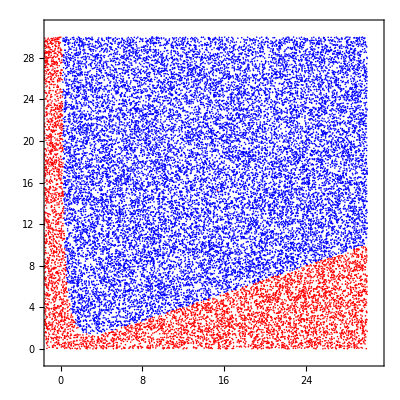

```mathematica
ListPlot[{Viable,NoViable},AspectRatio->1,PlotRange->{{-1,31},{-1,31}},Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Blue,Red},PlotLegends->{MaTeX["\\text{Viables}",Magnification->1.3],MaTeX["\\text{No viables}",Magnification->1.3]},Axes->False]
```

```mathematica
p=1;
xmin=-30;
xmax=30;
```

```mathematica
ρ[x_]:=(xmax-xmin)(x/n)^p+xmin
Ρ[x_]:=Ceiling[n((x-xmin)/(xmax-xmin))^(1/p)];
```

```mathematica
n=100;
Lineas=Table[Line[{{ρ[k],0},{ρ[k],30}}],{k,1,n}];
Lineas2=Table[Line[{{0,30 k/100},{30,30 k/100}}],{k,1,100}];
```

```mathematica
Tolerancia=ListPlot[{Viable,NoViable},AspectRatio->1,PlotRange->{{0,30},{0,30}},Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Blue,Red},PlotLegends->{MaTeX["\\text{Viables}",Magnification->1.3],MaTeX["\\text{No viables}",Magnification->1.3]},Axes->False,Epilog->{Lineas,Lineas2}];
```

```mathematica
antialias[g_]:=ImageResize[Rasterize[g,"Image",ImageResolution->300],Scaled[1]]
```

```mathematica
Export["Tolerancia.jpg",antialias[Show[Tolerancia]]];
```

### Analytical approximation of the region

-Graphics-

-Graphics-

```mathematica
n=200;
p=1;
Matriz1=Table[0,n,n];
Matriz2=Table[0,n,n];
For[i=1,i<=Length[NoViable],i++,Matriz1[[Ρ[NoViable[[i,1]]],Ρ[NoViable[[i,2]]]]]=1;]
For[i=1,i<=Length[Viable],i++,Matriz2[[Ρ[Viable[[i,1]]],Ρ[Viable[[i,2]]]]]=1;]
Matriz=Table[Matriz1[[i,j]]Matriz2[[i,j]],{i,1,n},{j,1,n}];
```

```mathematica
BoundaryOfRegion1=DeleteDuplicates@DeleteCases[Table[If[Matriz[[Ρ[Viable[[i,1]]],Ρ[Viable[[i,2]]]]]==1&&!(7<Viable[[i,1]]<8||0<Viable[[i,1]]<0.2),ρ@Ρ@Viable[[i]]],{i,1,Length[Viable]}],Null];
Length[BoundaryOfRegion1]
```

64

```mathematica
BoundaryOfRegion2=DeleteDuplicates@DeleteCases[Table[If[Matriz[[Ρ[NoViable[[i,1]]],Ρ[NoViable[[i,2]]]]]==1&&!(7<NoViable[[i,1]]<8||0<NoViable[[i,1]]<0.2),ρ@Ρ@NoViable[[i]]],{i,1,Length[NoViable]}],Null];
Length[BoundaryOfRegion2]
```

46

```mathematica
BoundaryOfRegion=DeleteDuplicates[Intersection[BoundaryOfRegion1,BoundaryOfRegion2]];
Length[BoundaryOfRegion]
```

45

```mathematica
B=Union@AppendTo[DeleteCases[Table[If[BoundaryOfRegion[[i-1,1]]!=BoundaryOfRegion[[i,1]],BoundaryOfRegion[[i]]],{i,2,Length[BoundaryOfRegion]}],Null],BoundaryOfRegion[[1]]];
```

Set::write: Tag DeleteCases in DeleteCases[{{3/5,36/5},Null,Null,Null,Null,Null,Null,Null,Null,{9/10,57/10},«34»},Null] is Protected.

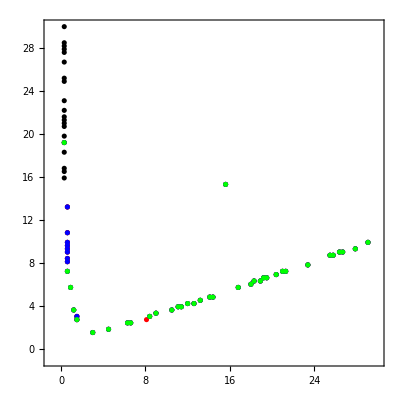

```mathematica
ListPlot[{BoundaryOfRegion1,BoundaryOfRegion2,BoundaryOfRegion,B},AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Black,Red,Blue,Green},Axes->False,PlotRange->{{-1,30},{-1,30}}]
```

```mathematica
fitAnalitical[x_]:=-x/3+2/3 √((36+x^4)/x^2)
```

```mathematica
weffMin=Table[{Viable[[i,1]],Viable[[i,2]],(weff/.Ωr->0/.SolViable[[i]])//Min},{i,1,Length[SolViable]}];
```

```mathematica
Beff=Union[DeleteCases[Table[If[AnyTrue[Table[(Ωm /. Ωr -> 0 /. Solutions[[i, 2, j]]), {j, 1, Length[Solutions[[i, 2]]]}], # >= -1 10^-12 &]&&Abs[(Min@(weff/.Ωr->0/.Solutions[[i, 2]])+1/3.)]<5 10^-3,Solutions[[i,1]]],{i,1,Length[Solutions]}],Null],N@{{√2 3^(1/4),fitAnalitical[√2 3^(1/4)]}}
];//AbsoluteTiming
```

{12.8801,Null}

```mathematica
Length@Beff
```

140

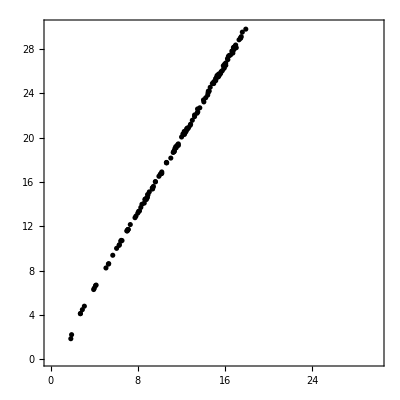

```mathematica
Show[ListPlot[Beff,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}],Plot[Prueba[[1]],{α,0,30},PlotLegends->Automatic]
]
```

```mathematica
Prueba=FindFormula[Beff,α,1,"Score",PerformanceGoal->"Quality",SpecificityGoal->"High"]
```

{-2.83124+3.08823 α-0.28684 α^2+0.027695 α^3-0.00128017 α^4+0.0000227959 α^5,4.2218}

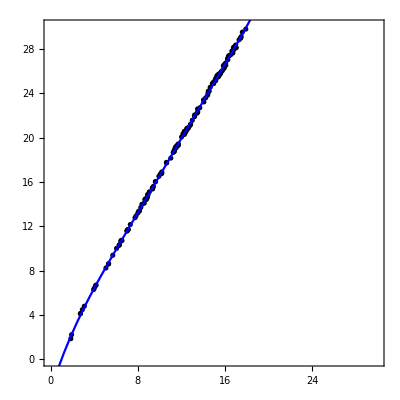

```mathematica
Show[
ListPlot[Beff,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}],
Plot[Prueba[[1]],{α,0,30},PlotStyle->{Blue},PlotLegends->LineLegend[{Directive[Dotted,Black],Directive[Thick,Blue]},{MaTeX["\\text{Boundary}",Magnification->1.3],MaTeX["\\text{Fit}"]}]]
]
```

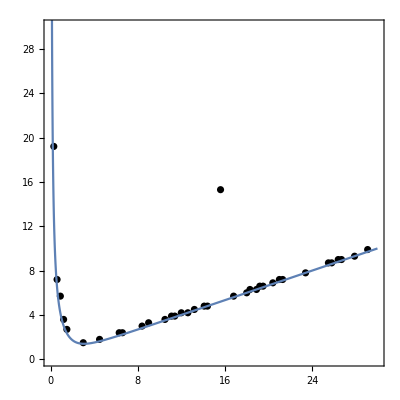

```mathematica
Show[
ListPlot[B,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}],
Plot[-α/3+2/3 √((36+α^4)/α^2),{α,0,30},PlotLegends->LineLegend[{Directive[Dotted,Black],Directive[Thick,Blue]},{MaTeX["\\text{Boundary}",Magnification->1.3],MaTeX["\\text{Fit}",Magnification->1.3]}],PlotRange->All]
]
```

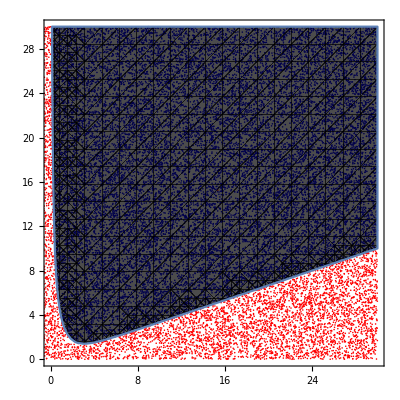

```mathematica
Show[
ListPlot[{Viable,NoViable},AspectRatio->1,PlotRange->{{0,30},{0,30}},Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Blue,Red},PlotLegends->{MaTeX["\\text{Viables}",Magnification->1.3],MaTeX["\\text{No viables}",Magnification->1.3]},Axes->False]
,
RegionPlot[β>-α/3+2/3 √((36+α^4)/α^2),{α,0,30},{β,0,30},PlotStyle->Directive[Black,Opacity[0.7]]]
]
```

### Fixed points classified

#### Anisotropic DE point

```mathematica
SolViable=DeleteCases[Table[If[Solutions[[i,1,2]]>fitAnalitical[Solutions[[i,1,1]]],Solutions[[i]]],{i,1,Length[Solutions]}],Null];//AbsoluteTiming
SolViable=DeleteCases[SolViable,{_,{}}];
Length[Solutions]
Length[SolViable]
```

{1.63918,Null}

50000

20467

```mathematica
Show[ListPlot[SolViable[[All,1]],AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotLegends->Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2)}"],π/4],{0.45,0.5}],FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.52], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}],RegionPlot[(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),{α,0,30},{β,0,30}]]
```

-Graphics-

```mathematica
(weffMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(weff/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
(wDEMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(wDE/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
(WmMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(Ωm/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
(weffMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(weff/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
(wDEMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(wDE/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
(WmMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(Ωm/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];)//AbsoluteTiming
```

{8.51912,Null}

{7.55728,Null}

{4.97215,Null}

{8.62006,Null}

{6.27424,Null}

{4.29974,Null}

```mathematica
weffgr=Show[
ListContourPlot[{weffMin},Frame->True,LabelStyle->{Black,12},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.5]&)/@Style["w_{\\rm eff}" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.5]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.5]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black}],

(*RegionPlot[{(α<0&&β>-fitAnalitical[-α])||(α>0&&β<fitAnalitical[α])},
{α,-30,30},{β,0,30},LabelStyle->{Black,15},PlotStyle->RGBColor[0.22,0.58,0.46], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}],*)

Plot[{If[α>√2 3^(1/4)&&Prueba[[1]]<30,Prueba[[1]]],If[fitAnalitical[α]<30&&-30<α<30,fitAnalitical[α]]},{α,0,30},PlotStyle->{Directive[Thickness[0.01],Red],Directive[Thickness[0.01],Black]},PlotLegends->{
Placed[LineLegend[{Directive[Thickness[0.01],Red]},{MaTeX["w_{\\text{eff}}=-\\frac{1}{3}",Magnification->1.5]}],{0.2,0.9}],


Placed[LineLegend[{Directive[Thickness[0.01],Black]},{MaTeX["\\text{\\color{white}{\\_}}",Magnification->1.2]}],{0.09,0.79}],

Placed[
Rotate[
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{\\colorbox{white}{\\textbf{(\\emph{DE-II})}}}"]
,0]
,{0.73,0.87}],


Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Non viable}"],0°],{0.25,0.35}],

Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{\\colorbox{white}{No accelerated}}"],58°],{0.79,0.45}],

Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{\\colorbox{white}{Accelerated}}"],85°],{0.58,0.58}]}
]
]
```

-Graphics-

```mathematica
Export["FixedPoints/weff.pdf",antialias@ weffgr];
```

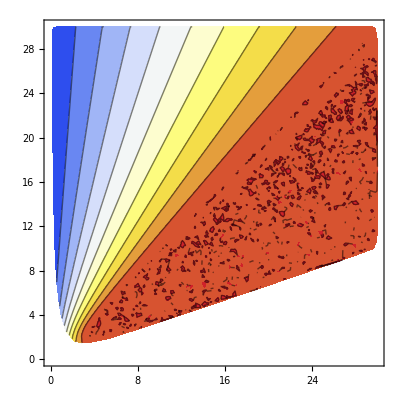

```mathematica
wDEgr=Show[
ListContourPlot[{wDEMin},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["w_{\\rm DE}" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black,15}]
]
```

```mathematica
Export["FixedPoints/wDE.pdf",antialias@wDEgr];
```

```mathematica
Wmgr=Show[
ListContourPlot[{WmMax},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\Omega_m" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black,15}]
]
```

-Graphics-

```mathematica
Export["FixedPoints/Wm.pdf",antialias@Wmgr];
```

```mathematica
weffAtractive=DeleteCases[
Table[
If[
Min[weffMin[[i,3]]<-1/3],
weffMin[[i]]
],{i,1,Length[weffMin]}
]
,Null];
WmAtractive=DeleteCases[
Table[
If[
Min[weffMin[[i,3]]<-1/3],
WmMax[[i]]
],{i,1,Length[weffMin]}
]
,Null];
```

```mathematica
WmAtractivegr=Show[ListContourPlot[{WmAtractive},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\Omega_m"]],Right],ColorFunction->"TemperatureMap",AspectRatio->1,PlotRange->{{0,30},{0,30}},FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]}],RegionPlot[(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),{α,0,30},{β,0,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotLegends->Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2) without accelerated expansion}"],40°],{0.55,0.45}],FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.1], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]]
```

-Graphics-

```mathematica
weffAtractgr=Show[ListContourPlot[{weffAtractive},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["w_{\\text{DE}}\\simeq w_{\\text{eff}}"]],Right],ColorFunction->"TemperatureMap",AspectRatio->1,PlotRange->{{0,30},{0,30}},FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]}],RegionPlot[(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),{α,0,30},{β,0,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotLegends->Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2) without accelerated expansion}"],40°],{0.55,0.45}],FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.1], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]]
```

-Graphics-

```mathematica
Export["FixedPoints/WeffAttractive.pdf",antialias@weffAtractgr];
```

```mathematica
ClasifyRegion=Show[RegionPlot[((α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)))&&Abs[α]<√2 3^(1/4),{α,-3,10},{β,0,30},LabelStyle->{Black,12},FrameLabel->{(MaTeX[#,Magnification->1.5]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.5]&)/@Style["\\beta"]},PlotStyle->RGBColor[0.22,0.58,0.46], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},Epilog->{{Directive[RGBColor[0.92,0.77,0.32],Dashed,Thickness[0.01]],Line[{{√2 3^(1/4),0},{√2 3^(1/4),(-(√2 3^(1/4))/3+2/3 √((36+(√2 3^(1/4))^4)/((√2 3^(1/4))^2)))}}],Line[{{-√2 3^(1/4),30},{-√2 3^(1/4),0}}]}}],RegionPlot[{(α<0&&β<-α/3-2/3 √((36+α^4)/α^2))||(α>0&&β>-α/3+2/3 √((36+α^4)/α^2))&&(β>Prueba[[1]])},
{α,-3,10},{β,0,30},LabelStyle->{Black,15},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.52],PlotRange->All, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}],Plot[{If[α>√2 3^(1/4)&&Prueba[[1]]<30,Prueba[[1]]],If[fitAnalitical[α]<30&&Abs[α]<√2 3^(1/4),fitAnalitical[α]]},{α,0,10},PlotStyle->{Directive[Thickness[0.01],Dashed,Red],Directive[Thickness[0.01],Black]}
,PlotLegends->{(*
Placed[LineLegend[{Directive[Dashed,Thickness[0.01],Red]},{MaTeX["w_{\\text{eff}}=-\\frac{1}{3}",Magnification->1.2]}],{0.25,0.9}],
Placed[LineLegend[{Directive[Dashed,Thickness[0.01],RGBColor[0.92,0.77,0.32]]},{MaTeX["w_{\\text{eff}}=-\\frac{1}{3}",Magnification->1.2]}],{0.25,0.8}],
Placed[LineLegend[{Directive[Thickness[0.01],Black]},{MaTeX["\\color[rgb]{0.22,0.58,0.46}{w_{\\text{eff}}=-\\frac{1}{3}}",Magnification->1.2]}],{0.25,0.7}],*)

Placed[
Rotate[
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{\\colorbox{white}{\\textbf{(\\emph{DE-II})}}}"]
,0]
,{0.6,0.6}],Placed[
Rotate[
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{\\colorbox{white}{\\textbf{(\\emph{DE-I})}}}"]
,0]
,{0.21,0.1}](*,


Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{No accelerated}"],0°],{0.25,0.35}]
,

Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{No accelerated}"],0°],{0.82,0.08}],

Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{No accelerated}"],58°],{0.79,0.45}],

Placed[Rotate[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Accelerated}"],85°],{0.58,0.58}]*)}
]
]
```

-Graphics-

```mathematica
Export["FixedPoints/ClasifyRegion.pdf",ClasifyRegion];
```

## Stability numerical analysis

## Anisotric DE

#### Stability Calculus

-Graphics-

```mathematica
JacobianMaTrix={};
```

```mathematica
JM=(D[system, {{x, y, z, Σ, Ωr}}]/.Ωr->0);
```

```mathematica
JacobianMaTrix = Table[
                   
                              (JM /. { α -> SolViable[[n, 1, 1]], β -> SolViable[[n, 1, 2]]})/. SolViable[[n, 2]]
                             

                       , {n, 1, Length[SolViable]}]; // AbsoluteTiming
Export["Stability/JacobianMaTriX.dat", JacobianMaTrix, "CSV", OverwriteTarget -> "KeepBoth"];
```

{27.9157,Null}

```mathematica
EigenSystem=Table[
       Table[
         Eigensystem[JacobianMaTrix[[j, i]]], {i, 1, Length[JacobianMaTrix[[j]]]}
         ]
        , {j, 1 , Length[JacobianMaTrix]}]; // AbsoluteTiming
```

{3.42288,Null}

```mathematica
Export["Stability/EygenSystem.dat", EigenSystem, "CSV"];
```

#### Sign of eigen values depending on α and β values

-Graphics-

```mathematica
Length[EigenSystem]==Length[SolViable]
```

True

```mathematica
l=Table[
If[AnyTrue[Sign@Re@EigenSystem[[i,All,1]],AllTrue[#,#<0&]&],{SolViable[[i,1,1]],SolViable[[i,1,2]],-1},{SolViable[[i,1,1]],SolViable[[i,1,2]],1}],{i,1,Length[SolViable]}
];//AbsoluteTiming
```

{3.9408,Null}

```mathematica
{Length[Select[l,#[[3]]==1&]],Length@Select[l,#[[3]]==-1&]}
```

{0,20467}

```mathematica
legend=SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"All negative","Otherwise"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}](*,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{\\{1||2||3||4||5\\}}]"]*),LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
```

```mathematica
lll=ListPlot[Drop[l,None,{3}],Frame->True,PlotLegends->Placed[legend,Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.5]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.5]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},FrameStyle->Directive[Black,12],LabelStyle->{Black,12}]
```

-Graphics-

```mathematica
Export["FixedPoints/EigenValuesDEAnI.pdf",antialias@lll];
```